# Diagrams for b->cl+inv with ALPs

```mathematica
$LoadAddOns={"FeynArts"};
Get["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
$FAVerbose = 0;
```

```mathematica
$CKM = True;
```

```mathematica
LoadModel["ALP"]
```

{ALP}

## SM

```mathematica
topSM = CreateTopologies[0, 1-> 3, ExcludeTopologies-> {WFCorrections}];
```

```mathematica
diagSM = InsertFields[topSM, {F[4, {3}]}-> {F[3, {2}],F[2, {3}], -F[1, {3}]}, Model-> "ALP", GenericModel-> "ALP",ExcludeParticles->S[3],  InsertionLevel->{Classes}];
```

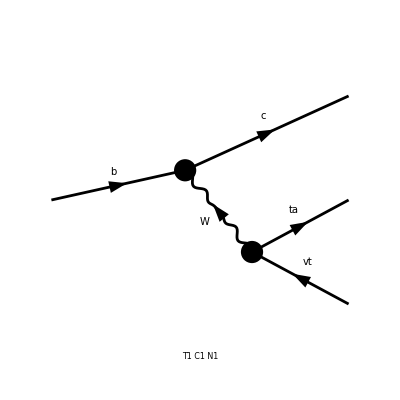

```mathematica
Paint[diagSM];
```

```mathematica
ampSM = FCFAConvert[CreateFeynAmp[diagSM, Truncated-> False], IncomingMomenta-> {pb}, OutgoingMomenta-> {pc, pl, pν, pa}, DropSumOver->True,UndoChiralSplittings->True,SMP->True]
```

{1/((OverBar[pl]+OverBar[pν])^2-m_W^2)(ḡ)^Lor1Lor2 (φ(OverBar[pl],MTA)).(ⅈ gc30 (γ̄)^Lor2.(γ̄)^7).(φ(-OverBar[pν])) (φ(OverBar[pc],m_c)).(ⅈ gc27(2,3) (γ̄)^Lor1.(γ̄)^7 δ_Col1Col2).(φ(OverBar[pb],m_b))}

## One-loop diagrams

```mathematica
top1to3 = CreateTopologies[1, 1-> 3, ExcludeTopologies-> {WFCorrections}];
```

```mathematica
diag1to3 = InsertFields[top1to3, {F[4, {3}]}-> {F[3, {2}],F[2, {3}], -F[1, {3}]}, Model-> "ALP", GenericModel-> "ALP",ExcludeParticles->S[3],  InsertionLevel->{Classes}, LastSelections-> S[4]];
```

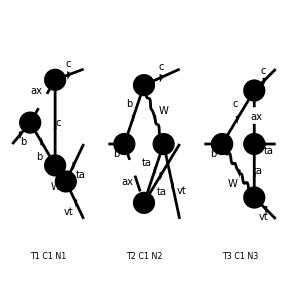

```mathematica
Paint[diag1to3];
```

## abc loop

```mathematica
diagabc = DiagramExtract[diag1to3, 1];
```

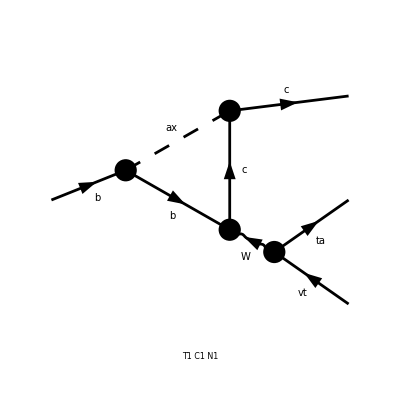

```mathematica
Paint[diagabc];
```

```mathematica
ampabc = FCFAConvert[CreateFeynAmp[diagabc, Truncated-> False], IncomingMomenta-> {pb}, OutgoingMomenta-> {pc, pl, pν}, LoopMomenta-> {k}, ChangeDimension-> D, DropSumOver->True,UndoChiralSplittings->True,SMP->True]
```

{-(ⅈ g^Lor1Lor2 (φ(pl,MTA)).(ⅈ gc30 γ^Lor1.(γ̄)^7).(φ(-pν)) (φ(pc,m_c)).(ⅈ gc8L (γ̄)^7+ⅈ gc8R (γ̄)^6).(m_c+γ·(pc-k)).(ⅈ gc27(2,3) γ^Lor2.(γ̄)^7 δ_Col1Col2).(m_b+γ·(-k+pc+pl+pν)).(ⅈ gc6L (γ̄)^7+ⅈ gc6R (γ̄)^6).(φ(pb,m_b)))/(16 π^4 ((-pl-pν)^2-m_W^2) (k^2-Ma^2).((k-pc)^2-m_c^2).((k-pc-pl-pν)^2-m_b^2))}

```mathematica
Simplify[Contract[ampabc/.gc8L-> -gc8R/.gc6L->-gc6R]]
```

{(ⅈ gc30 gc27(2,3) δ_Col1Col2 (φ(pl,MTA)).γ^Lor2.(γ̄)^7.(φ(-pν)) (φ(pc,m_c)).(ⅈ gc8R ((γ̄)^6-(γ̄)^7)).(m_c+γ·(pc-k)).γ^Lor2.(γ̄)^7.(m_b+γ·(-k+pc+pl+pν)).(ⅈ gc6R ((γ̄)^6-(γ̄)^7)).(φ(pb,m_b)))/(16 π^4 ((-pl-pν)^2-m_W^2) (k^2-Ma^2).((k-pc)^2-m_c^2).((k-pc-pl-pν)^2-m_b^2))}

## abl loop

```mathematica
diagabl = DiagramExtract[diag1to3, 2];
```

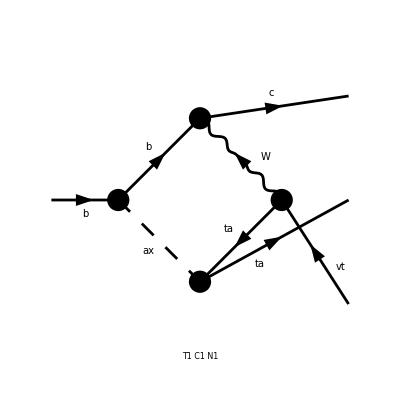

```mathematica
Paint[diagabl];
```

```mathematica
ampabl = FCFAConvert[CreateFeynAmp[diagabl, Truncated-> False], IncomingMomenta-> {pb}, OutgoingMomenta-> {pc, pl, pν}, LoopMomenta-> {k}, ChangeDimension-> D, DropSumOver->True,UndoChiralSplittings->True,SMP->True]
```

{-((ⅈ g^Lor1Lor2 (φ(pl,MTA)).(ⅈ gc7L (γ̄)^7+ⅈ gc7R (γ̄)^6).(γ·(k-pc-pν)+MTA).(ⅈ gc30 γ^Lor2.(γ̄)^7).(φ(-pν)) (φ(pc,m_c)).(ⅈ gc27(2,3) γ^Lor1.(γ̄)^7 δ_Col1Col2).(m_b+γ·k).(ⅈ gc6L (γ̄)^7+ⅈ gc6R (γ̄)^6).(φ(pb,m_b)))/(16 π^4 (k^2-m_b^2).((k-pc)^2-m_W^2).((k-pc-pν)^2-MTA^2).((k-pc-pl-pν)^2-Ma^2)))}

```mathematica
Simplify[Contract[ampabl/.gc7L-> -gc7R/.gc6L->-gc6R]/.k->l+pc+pν+pl]
```

{(ⅈ gc30 gc27(2,3) δ_Col1Col2 (φ(pl,MTA)).(ⅈ gc7R ((γ̄)^6-(γ̄)^7)).(γ·(l+pl)+MTA).γ^Lor2.(γ̄)^7.(φ(-pν)) (φ(pc,m_c)).γ^Lor2.(γ̄)^7.(m_b+γ·(l+pc+pl+pν)).(ⅈ gc6R ((γ̄)^6-(γ̄)^7)).(φ(pb,m_b)))/(16 π^4 ((l+pc+pl+pν)^2-m_b^2).((l+pl+pν)^2-m_W^2).((l+pl)^2-MTA^2).(l^2-Ma^2))}

## acl loop

```mathematica
diagacl = DiagramExtract[diag1to3, 3];
```

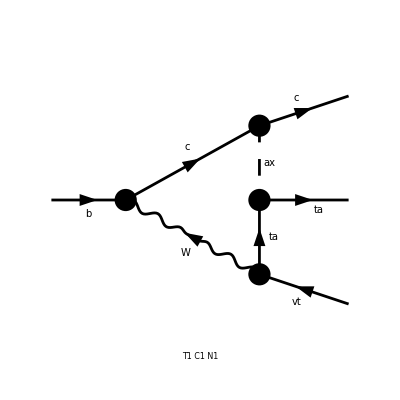

```mathematica
Paint[diagacl];
```

```mathematica
ampacl = FCFAConvert[CreateFeynAmp[diagacl, Truncated-> False], IncomingMomenta-> {pb}, OutgoingMomenta-> {pc,pl, pν}, LoopMomenta-> {k}, ChangeDimension-> D, DropSumOver->True,UndoChiralSplittings->True,SMP->True]
```

{-(ⅈ g^Lor1Lor2 (φ(pl,MTA)).(ⅈ gc7L (γ̄)^7+ⅈ gc7R (γ̄)^6).(γ·(-k+pc+pl)+MTA).(ⅈ gc30 γ^Lor2.(γ̄)^7).(φ(-pν)) (φ(pc,m_c)).(ⅈ gc8L (γ̄)^7 δ_Col1Col2+ⅈ gc8R (γ̄)^6 δ_Col1Col2).(m_c+γ·k).(ⅈ gc27(2,3) γ^Lor1.(γ̄)^7).(φ(pb,m_b)))/(16 π^4 (k^2-m_c^2).((k-pc)^2-Ma^2).((k-pc-pl)^2-MTA^2).((k-pc-pl-pν)^2-m_W^2))}

```mathematica
Simplify[Contract[ampacl/.gc7L-> -gc7R/.gc8L->-gc8R]/.k->l+pc]
```

{(ⅈ gc30 gc27(2,3) (φ(pl,MTA)).(ⅈ gc7R ((γ̄)^6-(γ̄)^7)).(γ·(pl-l)+MTA).γ^Lor2.(γ̄)^7.(φ(-pν)) (φ(pc,m_c)).(ⅈ gc8R ((γ̄)^6-(γ̄)^7) δ_Col1Col2).(m_c+γ·(l+pc)).γ^Lor2.(γ̄)^7.(φ(pb,m_b)))/(16 π^4 ((l+pc)^2-m_c^2).(l^2-Ma^2).((l-pl)^2-MTA^2).((l-pl-pν)^2-m_W^2))}

## ALP emission

```mathematica
top1to4 = CreateTopologies[0, 1-> 4, ExcludeTopologies-> {WFCorrections}];
```

```mathematica
diag1to4 = InsertFields[top1to4, {F[4, {3}]}-> {F[3, {2}],F[2, {3}], -F[1, {3}], S[4]}, Model-> "ALP", GenericModel-> "ALP",ExcludeParticles->S[3],  InsertionLevel->{Classes}];
```

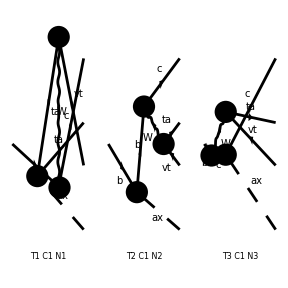

```mathematica
Paint[diag1to4];
```

## Lepton Emission

```mathematica
diagLepEmission = DiagramExtract[diag1to4, 1];
```

```mathematica
ampLepEmission = FCFAConvert[CreateFeynAmp[diagLepEmission, Truncated-> False], IncomingMomenta-> {pb}, OutgoingMomenta-> {pc, pl, pν, pa}, DropSumOver->True,UndoChiralSplittings->True,SMP->True]
```

{(ⅈ (ḡ)^Lor1Lor2 (φ(OverBar[pl],MTA)).(ⅈ gc7L (γ̄)^7+ⅈ gc7R (γ̄)^6).(γ̄·(OverBar[pa]+OverBar[pl])+MTA).(ⅈ gc30 (γ̄)^Lor2.(γ̄)^7).(φ(-OverBar[pν])) (φ(OverBar[pc],m_c)).(ⅈ gc27(2,3) (γ̄)^Lor1.(γ̄)^7 δ_Col1Col2).(φ(OverBar[pb],m_b)))/(((-OverBar[pa]-OverBar[pl])^2-MTA^2) ((OverBar[pa]+OverBar[pl]+OverBar[pν])^2-m_W^2))}

## B emission

```mathematica
diagBEmission = DiagramExtract[diag1to4, 2];
```

```mathematica
ampBEmission = FCFAConvert[CreateFeynAmp[diagBEmission, Truncated-> False], IncomingMomenta-> {pb}, OutgoingMomenta-> {pc, pl, pν, pa}, DropSumOver->True,UndoChiralSplittings->True,SMP->True]
```

{(ⅈ (ḡ)^Lor1Lor2 (φ(OverBar[pl],MTA)).(ⅈ gc30 (γ̄)^Lor2.(γ̄)^7).(φ(-OverBar[pν])) (φ(OverBar[pc],m_c)).(ⅈ gc27(2,3) (γ̄)^Lor1.(γ̄)^7 δ_Col1Col2).(γ̄·(OverBar[pc]+OverBar[pl]+OverBar[pν])+m_b).(ⅈ gc6L (γ̄)^7+ⅈ gc6R (γ̄)^6).(φ(OverBar[pb],m_b)))/(((OverBar[pl]+OverBar[pν])^2-m_W^2) ((-OverBar[pc]-OverBar[pl]-OverBar[pν])^2-m_b^2))}

## D emission

```mathematica
diagDEmission = DiagramExtract[diag1to4, 3];
```

```mathematica
ampDEmission = FCFAConvert[CreateFeynAmp[diagDEmission, Truncated-> False], IncomingMomenta-> {pb}, OutgoingMomenta-> {pc, pl, pν, pa}, DropSumOver->True,UndoChiralSplittings->True,SMP->True]
```

{(ⅈ (ḡ)^Lor1Lor2 (φ(OverBar[pl],MTA)).(ⅈ gc30 (γ̄)^Lor2.(γ̄)^7).(φ(-OverBar[pν])) (φ(OverBar[pc],m_c)).(ⅈ gc8L (γ̄)^7 δ_Col1Col2+ⅈ gc8R (γ̄)^6 δ_Col1Col2).(γ̄·(OverBar[pa]+OverBar[pc])+m_c).(ⅈ gc27(2,3) (γ̄)^Lor1.(γ̄)^7).(φ(OverBar[pb],m_b)))/(((-OverBar[pa]-OverBar[pc])^2-m_c^2) ((OverBar[pl]+OverBar[pν])^2-m_W^2))}